```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\tonnam_backup\Research_scratch\EG_Ag_2PDO\Ag100_allsides\bind_smaller_system\pull_50_windows\1_IC

```mathematica
log=OpenRead["timeseries.txt"];
```

```mathematica
data=ReadList[log,{Number,Number}];
```

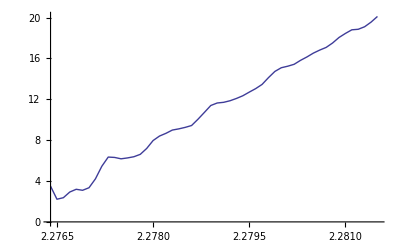

```mathematica
ListLinePlot[data[[1;;-1;;10]]]
```

```mathematica
CountDec=Reap[For[i=1,i≤10,i++,
datatest=data[[i;;-1;;10]];
Counter=0;
For[j=1,j<Length[datatest],j++,
If[datatest[[j+1,2]]<datatest[[j,2]],Counter+=1;];
];
Sow[Counter];
];][[2,1]]
```

{4,4,4,6,5,5,4,4,4,4}

```mathematica
CountDec[[10]]
```

4

```mathematica
data[[10;;-1;;10]]
```

{{22764900,2.64466},{22765900,2.19853},{22766900,2.51197},{22767900,2.82861},{22768900,3.05974},{22769900,3.87983},{22770900,4.92823},{22771900,5.97312},{22772900,6.50171},{22773900,6.16815},{22774900,6.12374},{22775900,6.27513},{22776900,6.50068},{22777900,6.8241},{22778900,7.61108},{22779900,8.40621},{22780900,8.71208},{22781900,8.91942},{22782900,9.22441},{22783900,9.38547},{22784900,9.36005},{22785900,9.70939},{22786900,10.4344},{22787900,11.0887},{22788900,11.6524},{22789900,11.7936},{22790900,11.8083},{22791900,12.0394},{22792900,12.272},{22793900,12.4952},{22794900,12.9488},{22795900,13.3845},{22796900,13.8028},{22797900,14.518},{22798900,14.9779},{22799900,15.2547},{22800900,15.3714},{22801900,15.5787},{22802900,16.0836},{22803900,16.4366},{22804900,16.7792},{22805900,17.1062},{22806900,17.4099},{22807900,17.8417},{22808900,18.383},{22809900,18.707},{22810900,18.9611},{22811900,19.075},{22812900,19.3768},{22813900,19.906},{22814900,20.4189}}